```mathematica
Clear["Global`*"];
startTime = SessionTime[];
```

Constant Declarations

```mathematica
(*
Assumptions:
shells are located around the origin and light rays never bend more than 90 degrees
*)
(* variables set to 64 digits of precision *)

TOL = 10^-8;
plutoRadius = 1195000`64; (* radius in meters *)

(* physical constants with increased arbitrary precision in mks units*)
NAvagadro=6.02214129`64*10^23;  (* Avagadro's number *)
R=8.3144621`64; (*J/mol K; universal gas constant*)
k = 1.3806488`64*10^-23; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67384`64*10^-11; (* universal gravitational constant *)

αN2=1.71`64*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas http://cccbdb.nist.gov/exp2.asp?casno=7727379 *)
μN2=0.0280134`64; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3`64; (* N/m^2; assumed surface pressure of Pluto == 3 microbars *)
T = 50.`64; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29`64*10^22; (* kg; mass of Pluto *)

distToObserver =5`64*10^12;(* TODO - average Pluto distance from Earth in m = 5*10^12 *)

(* make the atmosphere *)
layers = 100;
atmMin =plutoRadius;
atmMax = 1500000`64;
atmStep = (atmMax-atmMin)/layers;
```

```mathematica
Function Declarations
```

Declarations Function

```mathematica
(* local gravity as a function of r *)
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,h_,T_]:=p0 E^((-M Gravity[h+plutoRadius] h)/(R T));

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n given a temperature and pressure*)
LorentzLorenz[α_,p_,T_]:=SetPrecision[√(1+(4π NAvagadro α p)/(R T)),100]; 

(* indicies of refraction following the fit for the numbers provided in EY92 *)
EY92[r_]:=SetPrecision[1+2*10^105(r-1.3*10^5)^-18.75,100];

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value, and the attenuation coefficient αz *)
(* note that attenuation coefficient is represented here as αz rather than α because the letter also stands for mean polarizability, which is used elsewhere in this program; αz implies it's a function of z- the distance the beam of light travelled in the material *)
Shell[r_,n_,αz_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n,αz}; 

(* calculate the normal angle of a shell based on location, assuming shells centered at 0,0) *)
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]]; 

(* helper function to negate the y term of an xy pair for flipping atmospheric intersection points *)
FlipY[x_,y_]:=Return[{x,-y}];

(* refraction as a function of angles and rafractivity indicies *)
SnellsLaw[θin_,nin_,nout_]:=
If[nin == nout,
θin,
ArcSin[Sin[θin]nin/nout]
];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_,nTable_,αzTable_]:=Module[{r,center,nMax,nStep,n,αz,i},
atmosphere={};

Print["given a table of n values"];
i = 1;
Do[
{
n=nTable[[i]];
αz = αzTable[[i]];
atmosphere =Append[atmosphere,Shell[r,n,αz]];
i+=1;
},
{r,min,max,step}
];
];

(* make an atmosphere from a specified parameter file *)
MakeAtmosphereFromParams[params_]:=Module[{i,r,n,αz},
(* override the global atmosphere parameters with the specified ones *)
layers = Length[params];
atmMin =params[[1,1]];
atmMax = params[[Length[params],1]];
atmStep = (atmMax-atmMin)/layers;

(* create the proper shells and populate the atmosphere *)
paramAtmosphere = {};

Print[paramAtmosphere];
Do[
{
(* TODO adding 1 like this might cause an issue *)
r=ToExpression[params[[i,1]]];
n=SetPrecision[ToExpression[params[[i,2]]]+1,64];
αz=ToExpression[params[[i,3]]];
paramAtmosphere=Append[paramAtmosphere,Shell[r,n,αz]];
},
{i,1,layers}];
];

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{Opacity[0.5],Thin,atmosphere[[i,1]]}],{i,1,Length[atm]}];

MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

tList=Select[{t1,t2},(#∈Reals&&#>TOL)&] (* return only real positive time values *)
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius,difference,shellNum},
{
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
difference = Abs[posRadius-shellRadii[[i]]];
If[difference<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
]
};
rayLocation
]

(* updates the light position based on current position, direction, and shells *)
MoveLightRay[rayPath_,rayAngle_,atm_]:=Module[{location,tList,intersect,t,n2,αz,position,posRadius,shellNum,noIntersect,atEnd,distTravelledInShell},
extincted = False;
position = Last[rayPath];
posRadius = Norm[position];

location  = LocateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]];
},

(* only need to check the innermost shell *)
location == "inside",
{
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost and itself shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[Join[
FindNextShellIntersection[atm[[-2,3]],position,rayAngle],
FindNextShellIntersection[atm[[-1,3]],position,rayAngle]
]
];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell - the innermost shell represents the planet itself *)
{
extincted = True;
t =0;
},

(* if on some other shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)

(* check for non-intersection case *)
noIntersect = False;
atEnd = False;
If[t==Infinity,
If[Length[rayPath]==1,
noIntersect = True;
];
atEnd = True;
t=distToObserver; (* move the end of the light beam to the observer position *)
];

intersect = {t+position[[1]],Tan[rayAngle] t + position[[2]]};
position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
n2 = atm[[i,4]]; (* get the refractivity of the shell *)
If[!extincted && i>1,

αz=atm[[i-1,5]];, (* get the attenuation coefficient of the shell to the interior of this one *)

αz=0; (* if already extincted or in inner shell, this doesn't actually matter *)
];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 and αz = 0*)
n2 = 1.0;
αz=0;
];,
{i,Length[atm]}
];

(* if the light has not been entirely extincted yet, append the angle and final flux level to the appropriate lists *)
If[!extincted,
AppendTo[intersectionPoints,position];
Which[
noIntersect,
AppendTo[angleList,0.0];,

atEnd,
AppendTo[angleList,rayAngle];,

True,
AppendTo[angleList,Refract[intersectionPoints,angleList,n2]];

If[Length[intersectionPoints]>2 , (* if we're not at the starting point or first intersection point *)
distTravelledInShell = √((intersectionPoints[[Length[intersectionPoints],1]]-intersectionPoints[[Length[intersectionPoints]-1,1]])^2+(intersectionPoints[[Length[intersectionPoints],2]]-intersectionPoints[[Length[intersectionPoints]-1,2]])^2);,
distTravelledInShell=0;
];
currentRayFlux=BeerLambert[αz,currentRayFlux,distTravelledInShell]; (* calculate light extinction *)
];
];
];

(* refract based on entry and shell conditions using Snell's Law *)
Refract[rayPath_,angles_,n2_]:=Module[{newAngle,position,prevPosition,θ1,θ2,angle,interactionType},
position = Last[rayPath];
prevPosition = rayPath[[-2]];
angle = Last[angles];
interactionType = Null;

Which[
(* hitting the same shell again -- wait, I shouldn't actually need this, it should be included in the Snell's Law function *)
currentN==n2,
{
interactionType = "same shell";
newAngle = angle;
},

(* just grazed the top or bottom of a shell (no interaction), keep the angle the same *)
Abs[position[[1]]]<TOL,
{
interactionType = "grazed";
newAngle = angle;
(*Print["grazed shell with angle = " <> ToString[angle] <>" and starting y value of " <> ToString[yStart]];*)
},

(* hitting shell from outside in (radius decreasing) *)
Norm[position]<Norm[prevPosition],
{
interactionType = "outside in";

If [position[[2]]>0,
{ (* above the y = 0 line *)
θ1= Mod[π-NormalAngle[position]+angle,π/2];
If[π/2-Abs[θ1]<10^-5,
Print[θ1];
Print[position];
];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π+θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[NormalAngle[position]-π-angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π-θ2;
}
]
},

(* hitting shell from inside out *)
Norm[position]>Norm[prevPosition] || Norm[position]== Norm[prevPosition],
{
interactionType = "outside in";

If[position[[2]]>0,
{ (* above the y = zero line *)
θ1=Mod[NormalAngle[position]-angle,π/2];
If[π/2-Abs[θ1]<10^-5,
Print[θ1];
Print[position];
];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[angle-NormalAngle[position],π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]+θ2;
}
]
}
];
If[interactionType ≠ "grazed",
currentN=n2;
];

newAngle = Mod[newAngle,2π];
(* TODO - probably more elegent way to do the angle formatting, because I basically want all angles to be near zero for readability *)
If[newAngle> 3*π/4,
newAngle = newAngle-2*π;
];

newAngle
];

(* decrease the flux of a single light beam based on the linear approximation of the Beer-Lambert law *)
BeerLambert[αz_,flux_,z_]:=flux E^(-αz z);

(* count light rays on the observer plane using a constant-size linear collector assumption *)
MakeLightCurve[positions_,angles_,beamFluxes_,averagingLength_,averagingResolution_]:=Module[{upperEdge,lowerEdge,flux,collectedBeams, collectedAngles,upperIndex,lowerIndex,initializedList,collectorPos,sortedXValues,sortedYValues,yCheckStart,beamProperties,sortedAngles,sortedBeamFluxes,collectedBeamFluxes,i,edges,leftLCEdge,rightLCEdge},

beamProperties = Sort[{positions[[;;,1]],positions[[;;,2]],angles,beamFluxes}ᵀ,#1[[2]]>#2[[2]]&]; (* sort these by y value *)
sortedXValues = beamPropertiesᵀ[[1]];
sortedYValues = beamPropertiesᵀ[[2]];
sortedAngles = beamPropertiesᵀ[[3]];
sortedBeamFluxes = beamPropertiesᵀ[[4]];

upperEdge = First[sortedYValues];
lowerEdge = upperEdge-averagingLength;
flux = {}; (* list containing the total flux of the collected beams *)
collectedBeams = {}; (* list containing the actual y values of the collected beams - TODO - change the name of this*)
collectedAngles = {};
collectedBeamFluxes = {};
upperIndex = 0;
lowerIndex = 0;
i = 1;
initializedList = False;

While[True, (* move through the shadow plane and collect fluxes *)
Which[
!initializedList, (* initialize the list of collected beams *)
upperIndex = 1;
While[True, (* put beams into the list *)
If[i≤ Length[sortedYValues],
If[sortedYValues[[i]]<=upperEdge && sortedYValues[[i]] > lowerEdge,
AppendTo[collectedBeams,sortedYValues[[i]]];
AppendTo[collectedAngles,sortedAngles[[i]]];
AppendTo[collectedBeamFluxes,sortedBeamFluxes[[i]]];
lowerIndex = i;
i++;,
Break[];
],
Break[];
];
];
AppendTo[flux,{Mean[{upperEdge,lowerEdge}],Total[collectedBeamFluxes*Cos[collectedAngles]]}]; (* record the flux of collected beams (modified by the angle and multiplied by the individual fluxes later) *)
initializedList = True;,

lowerEdge ≥ Last[sortedYValues], (* all subsequent lists *)
upperEdge -=averagingResolution; (* move the collector *)
lowerEdge -=averagingResolution;

If[Length[collectedBeams]>0,
While[First[collectedBeams]>upperEdge, (* remove from the front of the list until boundaries agree *)
collectedBeams = Drop[collectedBeams,1];
collectedAngles = Drop[collectedAngles,1];
collectedBeamFluxes = Drop[collectedBeamFluxes,1];
If[Length[collectedBeams]==0,
Break[];
];
];
];

While[i≤Length[sortedYValues], (* put beams into the list *)
If[sortedYValues[[i]]<upperEdge && sortedYValues[[i]] > lowerEdge,
AppendTo[collectedBeams,sortedYValues[[i]]];
AppendTo[collectedAngles,sortedAngles[[i]]];
AppendTo[collectedBeamFluxes,sortedBeamFluxes[[i]]];
lowerIndex = i;
i++;,
Break[];
];
];
AppendTo[flux,{Mean[{upperEdge,lowerEdge}],Total[collectedBeamFluxes*Cos[collectedAngles]]}];, 

True, (* none of the other conditions is true anymore, we're at the end *)
Break[];
];
];

(* use the max light curve value to flatten out the top of the curve (accounting for problems with the collector position going off too far) *)
(* TODO- warning- this might remove diffraction effects at the edge of the curve *)
edges = Position[flux[[;;,2]],Max[flux[[;;,2]]]];
leftLCEdge = Min[edges];
rightLCEdge = Max[edges];
flux[[1;;leftLCEdge,2]] = Max[flux[[;;,2]]];
flux[[rightLCEdge;;Length[flux],2]] = Max[flux[[;;,2]]];

flux
];
```

Construct an Atmosphere

```mathematica
(* check to make sure that the discretization is proper; if not, fix it *)

If[Mod[atmMax-atmMin,atmStep]≠0,
{
atmMax=Floor[atmMax/atmStep]*atmStep;
Print["warning: atmosphere discretization is not integer- maximum radius corrected to "<> ToString[atmMax]];
}
];

LLnTable = Table[LorentzLorenz[αN2,Pressure[p0,μN2,h,T],T],{h,atmMin-plutoRadius,atmMax-plutoRadius,atmStep}]; (* refractivity table following the Lorentz-Lorenz form *)
EYnTable = Table[EY92[r],{r,atmMin,atmMax,atmStep}]; (* refractivitiy table following a power-law fit of the EY92 data (table 3a) *)
αzTable = Table[0.0000001,{r,atmMin,atmMax,atmStep}]; (* TODO - leaving these as some arbitrary value for now - attenuation coefficient for extinction *)
noRefraction = Table[1,{r,atmMin,atmMax,atmStep}];
noExtinction = Table[0,{r,atmMin,atmMax,atmStep}];
MakeAtmosphere[atmMin,atmMax,atmStep,EYnTable,noExtinction];

MakeAtmosphereFromParams[Import["/Users/Hosea/Dropbox (MIT)//Academic/12.ThG/AtmosphereCode/sampledAtmWithEYExtinction.tsv","TSV"]];
atmosphere=paramAtmosphere;
```

given a table of n values

{}

Simulate Light Rays

```mathematica
startingPosition = {}; (* store starting y coordiate *)
endingPosition = {}; (* store the ending y coordinate *)
totalRefraction = {}; (* store final angles from refraction *)
finalFlux = {}; (* store the final flux per beam as a fraction of the beam's original flux *)
dθOverdy={}; (* store a difference element of the above *)
atmGraphics = {}; (* store the graphics generated by the atmosphere model and the light rays *)
numIntersectionPoints = {}; (* store the number of intersections encountered by each light ray *)
extinctionY = 0; (* optimization thing to allow skipping over light rays that would be blocked by Pluto *)
beamsGenerated = 0; (* count the number of beams generated *)
beamsHittingAtm = 0;

maxLightY = 1.5; (* maximum multiplication factor for the y starting location of light beams, to be multiplied by maximum atmosphere specified *)
minLightY = 0;
stepLightY = -atmStep/atmMax; (* TODO - does this make sense to do? *)

Print["layers " <> ToString[layers]];

Do[
(*yStart = atmMin*yMultFact;(* parameterized to actual starting location *)*)
yStart = atmMax*yMultFact;(* parameterized to actual starting location *)
beamsGenerated = beamsGenerated + 1;
If[Abs[yStart]>Abs[extinctionY],
yMultTemp = PrintTemporary["y multiplicative factor " <> ToString[yMultFact]]; (* for tracking progress *)
origin = {-atmMax*1.25,yStart}; (* origin needs to be specified by doubles rather than ints *)
angle = 0; (* starting angle *)
currentN = 1.0; (* refractivity of the light ray's initial environment (vacuum) *)
currentRayFlux = 1.0; (* store the current flux of the ray that we're looking at, to be changed upon extinction *)

(* initialize lists of data *)
intersectionPoints = {origin};
angleList = {angle};

MoveLightRay[intersectionPoints,Last[angleList],atmosphere]; (* move the light ray up to the first atmosphere encounter *)

extincted = False;
(* keep on moving the light ray forward until it gets all the way through the atmosphere or is completely extincted *)
While[Norm[Last[intersectionPoints]]<= atmMax && !extincted,
MoveLightRay[intersectionPoints,Last[angleList],atmosphere];
];

(* put the results in the appropriate lists *)
If[!extincted,
AppendTo[startingPosition,{-atmMax*1.25,yStart}];
(*AppendTo[startingPosition,{-atmMax*1.25,-yStart}]*);

AppendTo[endingPosition,Last[intersectionPoints]];
(*AppendTo[endingPosition,{Last[intersectionPoints][[1]],-Last[intersectionPoints][[2]]}]*);

AppendTo[totalRefraction,Last[angleList]];
(*AppendTo[totalRefraction,-Last[angleList]]*);

AppendTo[finalFlux,currentRayFlux]; (* append twice for top and bottom versions *)
(*AppendTo[finalFlux,currentRayFlux]*);

(* removes the last intersection point because that one will be at the observer location... far, far away *)
intersectionWithoutLast = intersectionPoints[[1;;Length[intersectionPoints]-1]];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionWithoutLast]}],ListLinePlot[intersectionWithoutLast]}];
(*AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[Apply[FlipY,intersectionWithoutLast,{1}]]}],ListLinePlot[Apply[FlipY,intersectionWithoutLast,{1}]]}]*);

(*AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionPoints]}],ListLinePlot[intersectionPoints]}];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[Apply[FlipY,intersectionPoints,{1}]]}],ListLinePlot[Apply[FlipY,intersectionPoints,{1}]]}];*)

AppendTo[numIntersectionPoints,{yStart,Length[intersectionPoints]-2}]; (* minus 2 for start and end points*)
(*AppendTo[numIntersectionPoints,{-yStart,Length[intersectionPoints]-2}]*);

If[Length[startingPosition]>1,
AppendTo[dθOverdy,{yStart,(totalRefraction[[-2]]-totalRefraction[[-1]])/ (startingPosition[[-2,2]]-startingPosition[[-1,1]])}];
(*AppendTo[dθOverdy,{-yStart,-(totalRefraction[[-2]]-totalRefraction[[-1]])/(startingPosition[[-2,2]]-startingPosition[[-1,2]])}];*)
beamsHittingAtm = beamsHittingAtm + 1;
],

(* if the light was extincted, skip over the rest of the beams that would be, assuming symmetry *)
extinctionY = yStart;
];

NotebookDelete[yMultTemp];
],
{yMultFact,maxLightY,minLightY,stepLightY}
] 
Print["beams generated: " <> ToString[beamsGenerated]];
Print["beams hitting the atmosphere: " <> ToString[beamsHittingAtm]];
```

layers 191

beams generated: 376

beams hitting the atmosphere: 316

Graphics

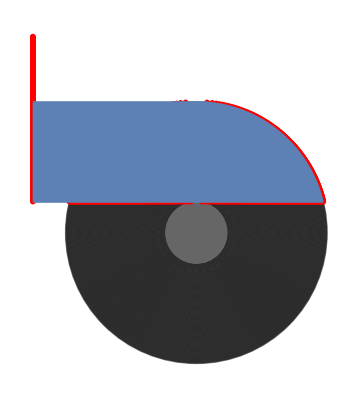

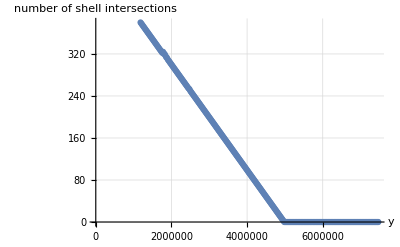

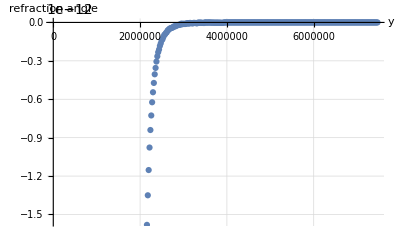

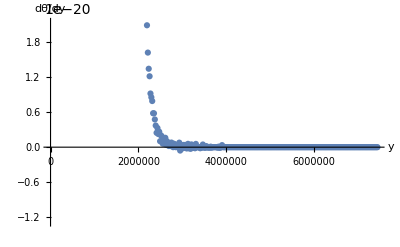

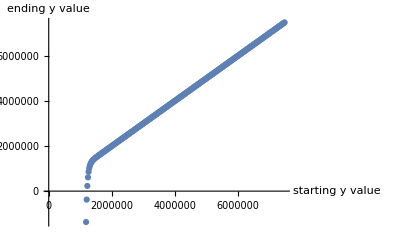

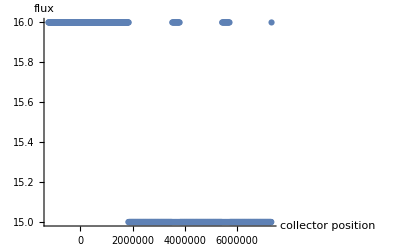

runtime: 189.5376350

```mathematica
(* graphics stuff starts here *)
plutoGraphic = Graphics[{GrayLevel[0.4],Disk[{0,0},atmMin]}];  (* graphic for the planet *)
Show[MakeAtmosphereGraphic[atmosphere],atmGraphics,plutoGraphic] (* shell graphic *)
ListPlot[numIntersectionPoints,AxesLabel-> {"y","number of shell intersections" },GridLines->Automatic]
ListPlot[ArrayReshape[Riffle[startingPosition[[;;,2]],totalRefraction],{Length[totalRefraction],2}],AxesLabel->{"y","refraction angle"},GridLines->Automatic]
ListPlot[dθOverdy,AxesLabel->{"y","dθ/dy"}]
ListPlot[ArrayReshape[Riffle[startingPosition[[;;,2]],endingPosition[[;;,2]]],{Length[endingPosition],2}],AxesLabel->{"starting y value","ending y value"}]
(*ListPlot[Sort[endingPosition[[;;,2]]],PlotLabel->"ending y values"]*)

(* make and plot light curve *)
orderOfMagY = Floor@Log[10,Abs[Min[endingPosition[[;;,2]]]]]; (* get the order of magnitude of the y values at collector position for the collector plot *)
ListPlot[MakeLightCurve[endingPosition,totalRefraction,finalFlux,3*10^(orderOfMagY-1),10^(orderOfMagY-2)],AxesLabel->{"collector position", "flux"}] 

Print["runtime: " <> ToString[SessionTime[]-startTime]];
```

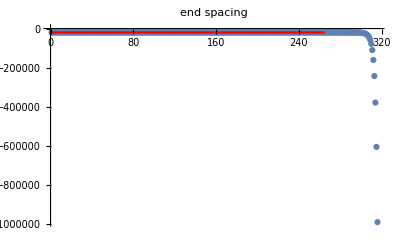

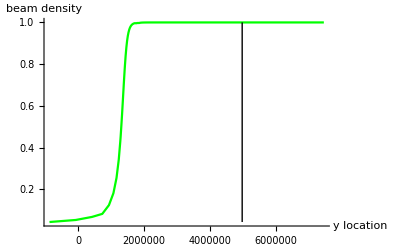

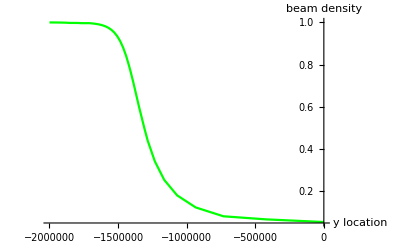

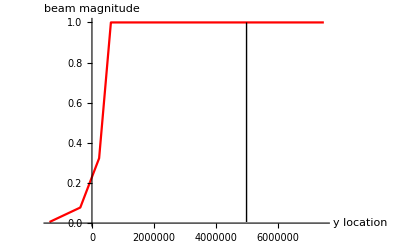

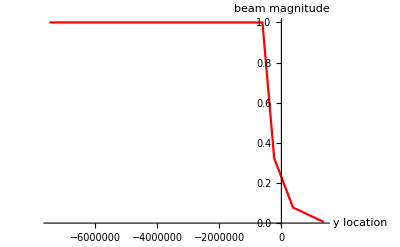

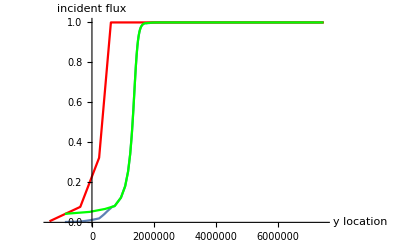

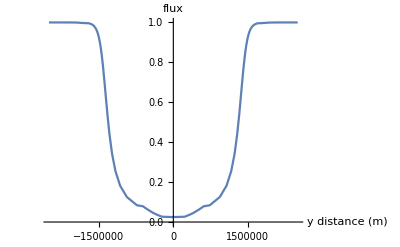

```mathematica
(* interpolated light curve portion *)

(* refraction interpolation on shadow plane *)

startSpacing = startingPosition[[1,2]]-startingPosition[[2,2]];
endSpacing = Sort[endingPosition[[;;,2]],Greater]; (* get and sort the y values of the ending position array *)
meanEndLocations = Mean[ArrayReshape[{endSpacing[[1;;Length[endSpacing]-1]],endSpacing[[2;;]]},{2,Length[endSpacing]-1}]];

(* get the shadow plane spacing *)
endSpacing = Drop[endingPosition[[;;,2]],1]; (* make the arrays equal length *)
endSpacing = endSpacing-endingPosition[[1;;Length[endingPosition]-1,2]];

(*endSpacing = -Abs[endSpacing]; (* TODO - this is pretty hackish (to remove positive values), maybe just have a cutoff at zero? *)
endSpacing=MedianFilter[endSpacing,5]; (* filter the endspacing to get rid of higher-order effects *)
*)
endSpacingInterp = Interpolation[endSpacing,InterpolationOrder->3];

Show[ListPlot[endSpacing,PlotRange->All,PlotLabel->"end spacing"],Plot[endSpacingInterp[x],{x,1,Length[endSpacing]},PlotStyle->Red]]

beamDensity = MedianFilter[-startSpacing/endSpacing,3]; (* get the beam density *)
(*beamDensity = -startSpacing/endSpacing; (* get the beam density *)*)

beamDensity=ArrayReshape[Riffle[meanEndLocations,beamDensity],{Length[meanEndLocations],2}];

(*beamDensity=-startSpacing/endSpacing;*)

beamDensity2 =beamDensity; (* for the other limb *)
beamDensity2[[;;,1]]=-beamDensity2[[;;,1]];

beamDensityInterp = Interpolation[beamDensity,InterpolationOrder->1] ;(* linearly interpolate the angle *)
beamDensityInterp2 = Interpolation[beamDensity2,InterpolationOrder->1];

(* beam density interpolation model *)
Show[Plot[beamDensityInterp[x],{x,Min[beamDensity[[;;,1]]],Max[beamDensity[[;;,1]]]},PlotStyle->Green,PlotRange->All],Graphics[Line[{{atmMax,Min[beamDensity[[;;,2]]]},{atmMax,Max[beamDensity[[;;,2]]]}}]],AxesLabel->{"y location","beam density"}]

Show[Plot[beamDensityInterp2[x],{x,-2*10^6,0},PlotStyle->Green,PlotRange->All],AxesLabel->{"y location","beam density"}]

(* flux interpolation model *)
(*beamMags=MedianFilter[finalFlux,4];*)
beamMags=finalFlux;
beamMags=ArrayReshape[Riffle[endingPosition[[;;,2]],beamMags],{Length[finalFlux],2}];

beamMags2=beamMags;
beamMags2[[;;,1]]=-beamMags2[[;;,1]];

magInterp=Interpolation[beamMags,InterpolationOrder->1];
magInterp2=Interpolation[beamMags2,InterpolationOrder->1];

Show[Plot[magInterp[x],{x,Min[beamMags[[;;,1]]],Max[beamMags[[;;,1]]]},PlotStyle->Red,PlotRange-> All],Graphics[Line[{{atmMax,Min[beamMags[[;;,2]]]},{atmMax,Max[beamMags[[;;,2]]]}}]],AxesLabel->{"y location","beam magnitude"}]

Show[Plot[magInterp2[x],{x,Min[beamMags2[[;;,1]]],Max[beamMags2[[;;,1]]]},PlotStyle->Red,PlotRange-> All],AxesLabel->{"y location","beam magnitude"}]
(* combined plot *)
Show[
Plot[magInterp[x]*beamDensityInterp[x],{x,Min[beamDensity[[;;,1]]],Max[beamDensity[[;;,1]]]},PlotRange->All,AxesLabel->{"y location","incident flux"}],
Plot[magInterp[x],{x,Min[beamMags[[;;,1]]],Max[beamMags[[;;,1]]]},PlotStyle->Red,PlotRange-> All],
Plot[beamDensityInterp[x],{x,Min[beamDensity[[;;,1]]],Max[beamDensity[[;;,1]]]},PlotStyle->Green,PlotRange->All]
]

(* TODO- probably need to normalize this plot *)
(* TODO - fix the downward bit coming from the extrapolation *)

twoLimbLC [x_]:=
Piecewise[
{
{magInterp2[x]*beamDensityInterp2[x],x≤magInterp[[1,1,1]]},
{magInterp[x]*beamDensityInterp[x]+magInterp2[x]*beamDensityInterp2[x],x>magInterp[[1,1,1]]&&x< magInterp2[[1,1,2]]},
{magInterp[x]*beamDensityInterp[x],x≥magInterp2[[1,1,2]]}
}
];

Plot[twoLimbLC[x],
(*{x,magInterp2[[1,1,1]],magInterp[[1,1,2]]}*)
{x,-2.5*10^6,2.5*10^6},
Exclusions->None,
AxesLabel->{"y distance (m)","flux"}
]

(*Show[
Plot[magInterp[x]*beamDensityInterp[x],{x,Min[beamMags[[;;,1]]],Max[beamMags[[;;,1]]]},PlotRange->All,AxesLabel->{"y location","incident flux"}],Plot[magInterp2[x]*beamDensityInterp2[x],{x,Min[beamDensity2[[;;,1]]],Max[beamDensity2[[;;,1]]]},PlotRange->All,AxesLabel->{"y location","incident flux"},PlotStyle->Green]
]
*)
(*Plot[magInterp[x]*beamDensityInterp[x]+magInterp[-x]*beamDensityInterp[-x],{x,Min[beamDensity[[;;,1]]],Max[beamDensity[[;;,1]]]},AxesLabel->{"y location","incident flux"},PlotRange->All(*{{-2*10^6,2*10^6},{0,1.1}}*)]*)
```

3.403435814278440799268376888755015084472604574635168605359200583558883705515360880696395845×10^-9

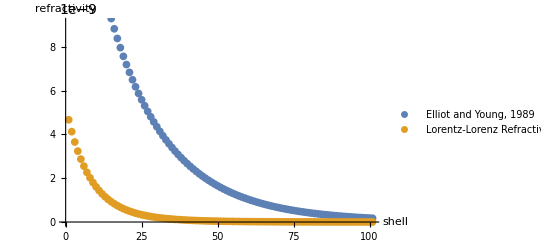

```mathematica
Mean[(EYnTable-LLnTable)/EYnTable]
ListPlot[{EYnTable-1,LLnTable-1},AxesLabel-> {"shell","refractivity"},PlotLegends->{"Elliot and Young, 1989","Lorentz-Lorenz Refractivity"}]
```